```mathematica
Clear["Global`*"]
```

```mathematica
nMat=1.444;
k0=2Pi/λ;
rMax=25;
rCore=8.2/2;
percn=0.0036;
c=3*10^8/1000/10^12;
η0=120*π;
nMax=nMat*(1+percn);
β=neff*k0;
```

```mathematica
u=Sqrt[(k0^2*(nMat(1+percn))^2)-β^2];
w=Sqrt[β^2-(k0*nMat)^2];
V=Sqrt[(k0*rCore)^2*((nMat*(1+percn))^2-nMat^2)];
n[r_]=(percn*HeavisideTheta[rCore-r]+1)*nMat;
```

```mathematica
hareqlp=Det[({{BesselJ[l,x], -BesselK[l,y]}, {x*D[BesselJ[l,x],x], -y*D[BesselK[l,y],y]}})]/.{x->u*rCore,y->w*rCore};
```

```mathematica
Manipulate[{Plot[hareqlp/.l->0/.λ->a,{neff,nMat,nMax},AxesOrigin->{nMat,0},ImageSize->Large],V/.λ->a},{a,0.9,1.55}]
```

```mathematica
solneff=FindRoot[hareqlp==0/.{λ->1.06,l->0},{neff,1.447}];
```

```mathematica
solB=Solve[A*BesselJ[l,x]-B*BesselK[l,y]==0/.{x->u*rCore,y->w*rCore}/.solneff/.{λ->1.06,l->0},B];
```

```mathematica
R[r_]=Piecewise[{{A*BesselJ[l,x]/.x->u*r/.solneff/.{λ->1.06,l->0},r<rCore},{B*BesselK[l,y]/.y->w*r/.solneff/.{λ->1.06,l->0},r≥rCore}}];
```

```mathematica
int[r_,ϕ_]=ComplexExpand[Abs[R[r]*Cos[ϕ*l]]^2]/.solB/.{A->1,l->0};
```

```mathematica
norm[r_,ϕ_]=int[r,ϕ]/Integrate[int[r,ϕ]*r,{r,0,rMax},{ϕ,0,2*π}];
```

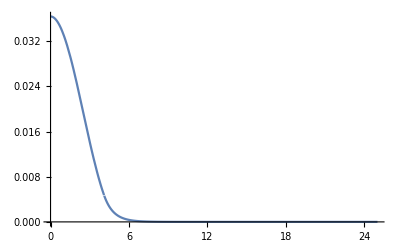

```mathematica
Plot[norm[r,0],{r,0,rMax},PlotRange->All]
```

```mathematica
ParametricPlot3D[{r*Cos[ϕ],r*Sin[ϕ],norm[r,ϕ][[1]]},{r,0,10},{ϕ,0,2*π},BoxRatios->{1, 1, 1},PlotRange->All,ImageSize->Large,Exclusions->{rCore},Mesh->100,MeshStyle->None,ColorFunction->"TemperatureMap"]
```

-Graphics3D-

```mathematica
(*Сравнить два решения: через характеристическое уравнение и через дискретизацию ППП (как на семинаре) данные для SMF28*)
(*решение через NDEigensystem*)
nsmf28=Import["SMF28.xlsx",Path->NotebookDirectory[]][[1]];
```

```mathematica
nsmf28=Delete[nsmf28,1];
```

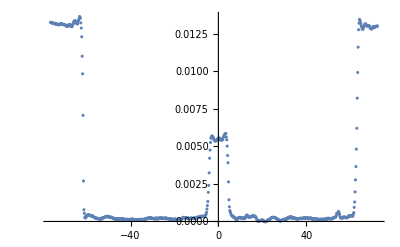

```mathematica
ListPlot[nsmf28]
```

```mathematica
intnsmf28=Interpolation[nsmf28,InterpolationOrder->1];FNsmf28Sim[r_]=(intnsmf28[r]+intnsmf28[-r])/2+nMat;
```

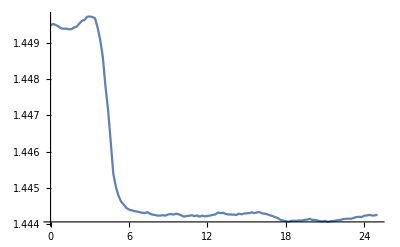

```mathematica
Plot[FNsmf28Sim[r],{r,0,rMax}]
```

```mathematica
{values,vectors}=NDEigensystem[(R''[r]+(1/r)*R'[r]+k0^2*(FNsmf28Sim[r])^2*R[r])/.λ->1.06,R[r],{r,0,rMax},100];
```

NDEigensystem::maxeigen: A maximum number of 41 eigenvalues and functions can be computed for this discretized system.

```mathematica
neffv=Sqrt[values]/k0/.λ->1.06;
neffvf=Chop[Select[neffv,((Re[#]>nMat)&&(Re[#]<1.450)&&(Im[#]<10^-10))&] ] ;
numbers=Table[Position[Re[neffv],neffvf[[i]]],{i,Length[neffvf]}]
```

{{{40}},{{41}}}

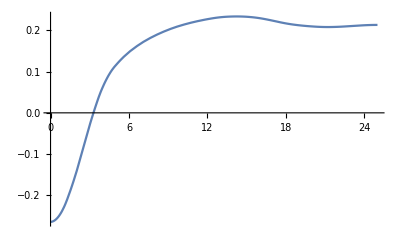

```mathematica
Plot[vectors[[40]],{r,0,rMax}]
```

```mathematica
(*решение через дискретизацию*)
```

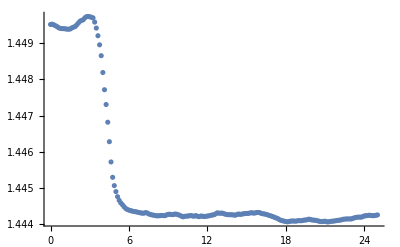

```mathematica
NN=201;
h=rMax/NN;
RIP=Array[FNsmf28Sim[#*rMax/NN]&,NN];
ListPlot[RIP, DataRange->{0,rMax}]
```

```mathematica
l=0;
λ=1.06;
```

```mathematica
D1=DiagonalMatrix[ConstantArray[-1/2,NN-1],-1]+DiagonalMatrix[ConstantArray[1/2,NN-1],1];
D1[[1]]=PadRight[{-3/2,2,-1/2},NN];
D1[[-1]]=PadLeft[{1/2,-2,3/2},NN];
D2=Normal[SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{NN,NN}]];
D2[[1]]=PadRight[{2,-5,4,-1},NN];
D2[[-1]]=PadLeft[{-1,4,-5,2},NN];
DivByr=Array[1/h/#&,NN];
shturmop=D2/h^2+1/h D1 DivByr-l^2DivByr^2 IdentityMatrix[NN]+k0^2 RIP^2 IdentityMatrix[NN];
{β,Modes}=Eigensystem[shturmop];
β=Sqrt[β];
```

```mathematica
TrueModesNEff=Chop[Select[β/k0,((Re[#]>nMat)&&(Re[#]<nMat*(1+percn))&&(Im[#]<10^-10))&] ]
svect=Table[First[NullSpace[shturmop-(TrueModesNEff[[i]]*k0)^2*IdentityMatrix[NN]]],{i,Length[TrueModesNEff]}];
```

{1.44786,1.44602,1.44407}

```mathematica
βRes={};
att=100;(*коэффициент, показывающий во сколько раз допустимо отличие по интенсивности*)
maxDer=100;
For[i=1,i<Length[svect],i++,
(*производная*)
dE=ListCorrelate[{-1,1},svect[[i]]];
dE=Insert[dE,svect[[i]][[-1]]-svect[[i]][[-2]],-1];
dE=dE/h;

If[MatchQ[Max[Abs[svect[[i]]^2]]/att-Abs[svect[[i]][[-5;;-1]]^2],{__?Positive}]&& MatchQ[Max[Abs[dE]]/maxDer-dE[[-5;;-1]],{__?Positive}],
βRes=Insert[βRes,TrueModesNEff[[i]],-1];
]
]
```

```mathematica
numbers=Table[Position[Re[β/k0],βRes[[i]]][[1]],{i,Length[βRes]}]
```

{{91}}

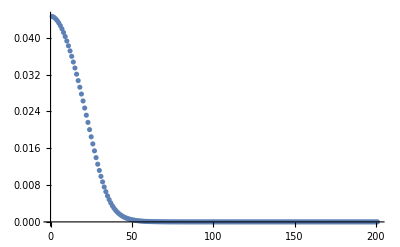

```mathematica
ListPlot[Abs[Modes[[91]]]^2,PlotRange->All]
```

```mathematica
(*решение через хар. уравнение для ступеньки выше*)
```

```mathematica
(*найти длину волны отсечки с помощью решения характеристического уравнения*)
```

```mathematica
(*Subscript[HE, 21]+Subscript[TM, 0m]=Subscript[LP, 1m],Subscript[HE, 21]+Subscript[TE, 0m]=Subscript[LP, 1m],
Subscript[LP, 01]=Subscript[HE, 11],
Subscript[LP, νm]=Subscript[EH, ν-1,m]±Subscript[HE, ν+1,m] при ν≥2, поэтому можно искать частоты отсечек для этих мод и брать максимальную*)
```

```mathematica
(*l=0*)
votsTETM=Table[BesselJZero[0,m],{m,10}];
(*l≥1 EH моды (знак плюс в решении квадратного уравнения отснсительно J'/J*)
votsEH=Table[Table[BesselJZero[l,m],{m,10}],{l,10}];
(*l=1 HE моды (знак минус в решении квадратного уравнения отснсительно J'/J*)
votsHE[1]=Table[BesselJZero[1,m],{m,10}];
(*l≥2 HE моды (знак минус в решении квадратного уравнения отснсительно J'/J*)
FindRoot[BesselJ[l-2,v]+(nMax^2-nMat^2)/(nMax^2+nMat^2)*BesselJ[l,v]==0/.l->3,{v,1}]
```

```mathematica
(*длина волны отсечки волокна*)
```

```mathematica
Plot[hareqlp/.{λ->1.06,l->0},{neff,nMat,nMax},AxesOrigin->{nMat,0}]
```